## 183Au

```mathematica
ClearAll["Global`*"]
```

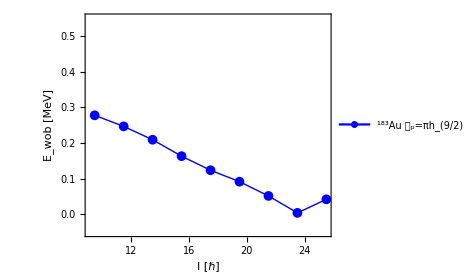

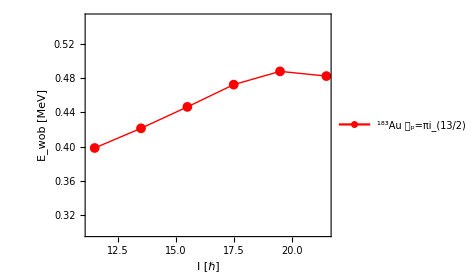

```mathematica
yrastEn1=Sort[{6242,5497,4760,4050,3358,2690,2063,1492,990,566,232,12.78}];
wob1En1=Sort[{5912,5133,4457,3796,3148,2540,1987,1488,1056}];
yrastSpin1=Table[i/2,{i,9,53,4}];
wob1Spin1=Table[i/2,{i,19,51,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+2]]+yrast[[i+3]])/1000},{i,1,Length[b1]}];
data1=wobbling[yrastEn1,wob1En1,wob1Spin1];
fig1=ListPlot[data1,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","183"],"Au 𝒬_p=πh_(9/2)"}]},{0.6,0.9}],ImageSize->350,PlotRange->{Full,{-0.05,0.55}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/183Au_1.pdf",fig1];
Show[fig1]
yrastEn2=Sort[{7848,7103,6375,5677,4986,4308,3655,3049,2492,1983,1530,1151,867,702}];
wob1En2=Sort[{4464,3840,3243,2684,2178,1739}];
yrastSpin2=Table[i/2,{i,13,65,4}];
wob1Spin2=Table[i/2,{i,23,43,4}];
data2=wobbling[yrastEn2,wob1En2,wob1Spin2];
fig2=ListPlot[data2,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Red},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","183"],"Au 𝒬_p=πi_(13/2)"}]},{0.6,0.9}],ImageSize->350,PlotRange->{Full,{0.3,0.55}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/183Au_2.pdf",fig2];
Show[fig2]
```